# ^135Pr - Study of the Energy Ellipsoid

## Classical description of the energy spectrum of the rotating system I=R+j

## The equations of motion for the system are:

### Piecewise[{{x_1^•=2(1-u)x_2 x_3, (a}, {x_2^•=2(x_1 u-v_0)x_3, (b}, {x_3^•=-2(x_1-v_0)x_2, (c}}]

Use the polar coordinate system to represent the coordinates x_1,x_2 and x_3.The notation x_k=I_k, where I is the angular momentum of the system.
By writing the components of the angular momentum (the total a.m. I) as a function of its components, in a polar coordinate system, then the energy function can be expressed in terms of those variables.

```mathematica
x1Second[spin_,theta_,fi_]:=spin*Sin[theta]*Sin[fi];
x2Second[spin_,theta_]:=spin*Cos[theta];
x3Second[spin_,theta_,fi_]:=spin*Sin[theta]*Cos[fi];
```

```mathematica
ParametricPlot3D[{x1Second[10,θ,ϕ],x2Second[10,θ],x3Second[10,θ,ϕ]},{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

## The energy function H’

The energy function is determined by a diagonalization procedure, with the help of the angular momentum components. 
With the components of the a.m. expressed in terms of the radius of the rotor’s a.m. sphere I, and the coordinates (spherical) (θ,ϕ), one can determine the energy function expression

## Problem approach

Consider the case of ℐ_1 as the maximal MOI.

The first step is to fix the maximal moment of inertia long one of the principal axes.
We fix it around the first axes. ℐ_1- max MOI. The following spherical representation of the angular momentum components is chosen:

-Graphics-

## Spherical coordinates for first-axis maximal MOI

```mathematica
x1First[spin_,theta_]:=spin*Cos[theta];
x2First[spin_,theta_,fi_]:=spin*Sin[theta]*Cos[fi];
x3First[spin_,theta_,fi_]:=spin*Sin[theta]*Sin[fi];
```

Fix the moments of inertia  ℐ_1, ℐ_2, ℐ_3

Fix the coupling angle θ

Fix the angular momentum value of the odd-particle (j)

Fix a spin value for the total system

## Constants

```mathematica
spinvalue=17/2;
j=13/2;
I1=89;
I2=12;
I3=48;
A1=1/(2*I1);
A2=1/(2*I2);
A3=1/(2*I3);
Subscript[θ, cpl]=-71*π/180;
```

## Inertial functions

The inertial terms which enter in the expression of the Hamiltonian H’

```mathematica
Afct[spin_,oddspin_,a1_,a2_,th_]:=a2(1-(oddspin*Sin[th])/spin)-a1;
ufct[spin_,oddspin_,a1_,a2_,a3_,th_]:=(a3-a1)/Afct[spin,oddspin,a1,a2,th];
v0fct[spin_,oddspin_,a1_,a2_,th_]:=-(a1*oddspin*Cos[th])/Afct[spin,oddspin,a1,a2,th];
vfct[spin_,oddspin_,a1_,a2_,th_]:=v0fct[spin,oddspin,a1,a2,th]/spin;
```

## Declare constant inertial functions

```mathematica
u[spin_]:=ufct[spin,j,A1,A2,A3,Subscript[θ, cpl]];
v0[spin_]:=v0fct[spin,j,A1,A2,Subscript[θ, cpl]];
v[spin_]:=vfct[spin,j,A1,A2,Subscript[θ, cpl]];
```

```mathematica
EnHA[spin_,theta_,fi_]:=(Cos[fi]^2+u[spin]*Sin[fi]^2)*(spin^2-x1First[spin,theta]^2)+2*v0[spin]*x1First[spin,theta];
```

```mathematica
Manipulate[Show[SphericalPlot3D[EnHA[spini,x,y],{x,-π,π},{y,0,2π}],MaxRecursion->10,ImageSize->Large,Mesh->Full,Mesh->None,AxesLabel->{"θ","ϕ"},Epilog->Inset[Framed[Style[StringTemplate["I=``"][spini],20,Italic,Black,FontFamily->"Times New Roman"],Background->None],{Right,Bottom},{Right,Bottom}],LabelStyle->{14,Bold,Black,FontFamily->"Times New Roman"}],{spini,1,50,1.5}]
```

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
```

```mathematica
Manipulate[Show[ContourPlot[EnHA[spini,x,y],{x,0,π},{y,0,2π},ImageSize->Large,Mesh->None,FrameLabel->{"θ","ϕ"},PlotLegends->Automatic,ContourLabels->(Text[Style[#3,15.5,Italic,Bold,Black,FontFamily->"Times New Roman"],{#1,#2},Background->LightBlue]&),ColorFunction->CoolColor,Contours->10,LabelStyle->{17,Bold,Black,FontFamily->"Times New Roman"}]],{spini,7.5,30.5,2.5}]
```

## Show the stationary points for the energy plots

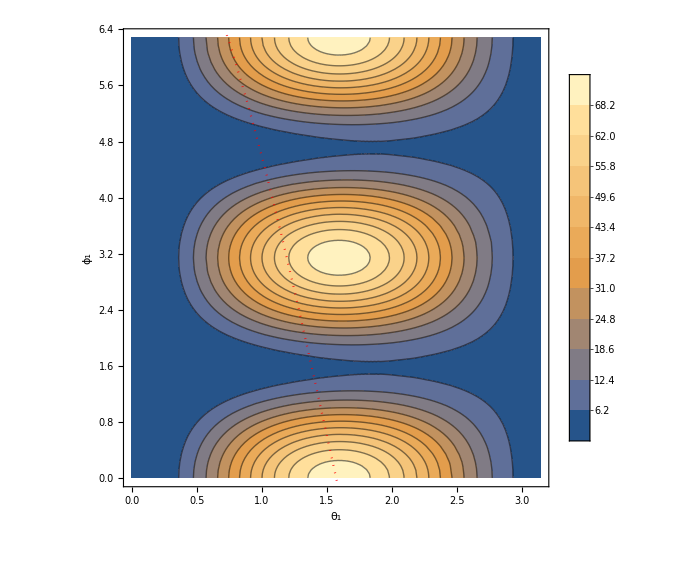

```mathematica
Show[ContourPlot[EnHA[spinvalue,x,y],{x,0,π},{y,0,2π},ImageSize->Large,Mesh->None,FrameLabel->{"θ_1","ϕ_1"},PlotLegends->Automatic,(*ContourLabels->(Text[Style[#3,15.5,Italic,Bold,Black,FontFamily->"Times New Roman"],{#1,#2},Background->LightBlue]&),*)Contours->11,LabelStyle->{17,Bold,Black,FontFamily->"Times New Roman"}],Plot[x1First[spinvalue,x],{x,0,2π},PlotStyle->{Red,Thick,Dotted}]]
```

## the minimum points

## C1) (x_1,ϕ_1) → (v_0/u,π/2)

```mathematica
fi1Min=N[π/2];
x1Min=N[v0[spinvalue]/u[spinvalue]];
θ1Min=N[ArcCos[x1Min/spinvalue]];
p1Min=Point[{θ1Min,fi1Min}];
```

## C2) (x_1,ϕ_1) → (v_0,0)

```mathematica
fi1Min2=0;
x1Min2=N[v0[spinvalue]];
θ1Min2=N[ArcCos[x1Min2/spinvalue]];
p1Min2=Point[{θ1Min2,fi1Min2}];
```